```mathematica
Sum[(n^j)*(pq-j-1),{j,0,pq-2}]
```

-(1-n^pq-pq+n pq)/(-1+n)^2

```mathematica
Simplify[-(1-n^pq-pq+n pq)/(-1+n)^2]
```

(-1+n^pq+pq-n pq)/(-1+n)^2

```mathematica
faux[n_]:=Binomial[n,Floor[n/2]]
```

```mathematica
ListPlot[{Labeled[2^Range[2,10],2^n ],Labeled[faux[Range[2,10]],Binomial[n,Floor[n/2]]]}]
```

-Graphics-

```mathematica
Export["/Users/jp/Documents/curvecomparison.pdf",%14,"PDF"]
```

/Users/jp/Documents/curvecomparison.pdf

```mathematica
Sum[((n^j)-1)/(n-1),{j,1,pq-1}]
```

(-1+n^pq+pq-n pq)/(-1+n)^2

```mathematica
Sum[n^j,{j,1,pq-1}]
```

(-n+n^pq)/(-1+n)

```mathematica
Simplify[Binomial[n,Floor[n/2]] + %6 + Binomial[n,Floor[n/2]]*Sum[n^j,{j,1,pq-1}]]
```

(-1+n^pq+pq-n pq+(-1+n) (-1+n^pq) Binomial[n,Floor[n/2]])/(-1+n)^2

```mathematica
f1[n_,pq_]:=(-1+n^pq+pq-n pq+(-1+n) (-1+n^pq) Binomial[n,Floor[n/2]])/(-1+n)^2
```

```mathematica
f2[n_,pq_]:=Binomial[n,Floor[n/2]]*n^(pq-1)
```

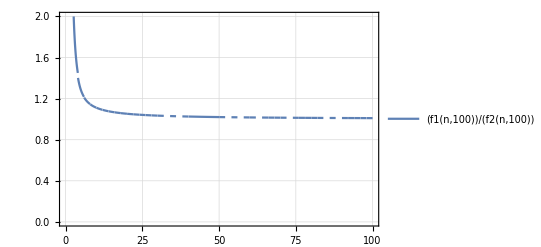

```mathematica
Plot[f1[n,100]/f2[n,100],{n,2,100},PlotTheme->"Detailed",PlotRange->{0,2}]
```

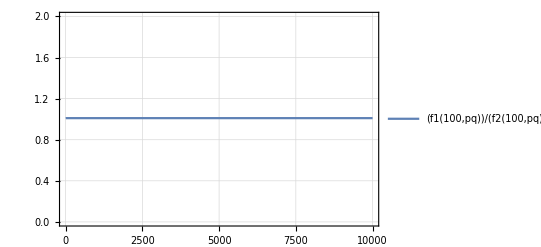

```mathematica
Plot[f1[100,pq]/f2[100,pq],{pq,2,10000},PlotTheme->"Detailed",PlotRange->{0,2}]
```

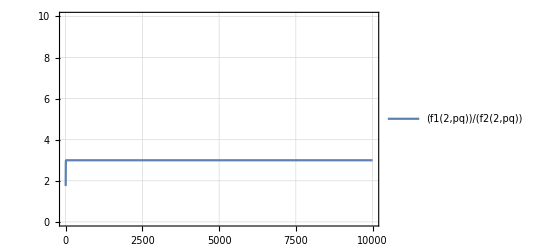

```mathematica
Plot[f1[2,pq]/f2[2,pq],{pq,2,10000},PlotTheme->"Detailed",PlotRange->{0,10}]
```

```mathematica
TeXForm[%10]
```

\frac{(n-1) \left(n^{\text{pq}}-1\right) \binom{n}{\left\lfloor \frac{n}{2}\right\rfloor
   }+n^{\text{pq}}-n \text{pq}+\text{pq}-1}{(n-1)^2}